## Compact Radial Coordinate

```mathematica
Clear["Global`*"]
M=1;
```

```mathematica
rH = M + √(M^2-a^2);
rStar = √(rr^2-rH^2);
compR =rStar/(1+rStar);
sol =Simplify[Solve[compR ==Rr,rr]];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
rPlus = rr/.sol[[2]];
rMinus = rr/.sol[[1]];
```

```mathematica
hPlus[g_]:= (-g[[1,4]]+√(g[[1,4]]^2-g[[1,1]]g[[4,4]]))/g[[1,1]]
hMinus[g_]:= (-g[[1,4]]-√(g[[1,4]]^2-g[[1,1]]g[[4,4]]))/g[[1,1]]
```

## Kerr Black Hole in a Swirling Universe

```mathematica
Δ =r^2-2 M r+a^2;
R=r^2+a^2(Cos[θ])^2;
ρ=(Δ*(Sin[θ])^2)^(1/2);
Σ=(r^2+a^2)-Δ*a^2*(Sin[θ])^2;
Ω=Δ*a*(Cos[θ])^2;
Ξ=r^2((Cos[θ])^2-3)+a^2(1+(Cos[θ])^2);
f0=R^4;
f1 =4 a*M*Ξ*Cos[θ] R^2;
f2=4 a^2 M^2 Ξ^2(Cos[θ])^2+Σ^2(Sin[θ])^4;
w0 = 2 a M r;
w1 =4(Cos[θ])(M a^4-r^4(r-2M)-Δ*a^2 r-a(r-M)Ω);
w2= 2M(3a r^5-a^5(r+2M)+2 a^3 r^2(r+3M)-r^3((Cos[θ])^2-6)Ω+a^2 Ω((Cos[θ])^2)(3r-2M)-6(r-M));
f =Simplify[ (f0+j*f1+j^2 f2)/(R^2 Σ(Sin[θ])^2)];
w=Simplify[(w0+j w1+j^2 w2)/Σ];
KBmetricPlus = {{w^2/f-ρ^2 f,0,0,w/f},{0,(f*Σ*(Sin[θ])^2)/Δ,0,0},{0,0,f*Σ*(Sin[θ])^2,0},{w/f,0,0,1/f}}/.r-> rPlus;
```

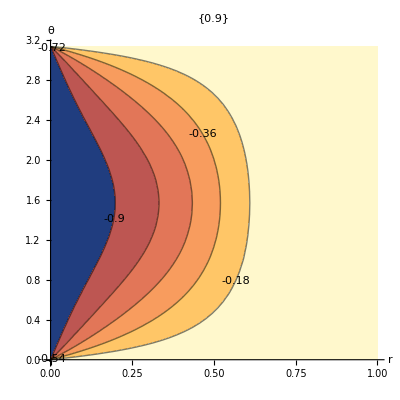
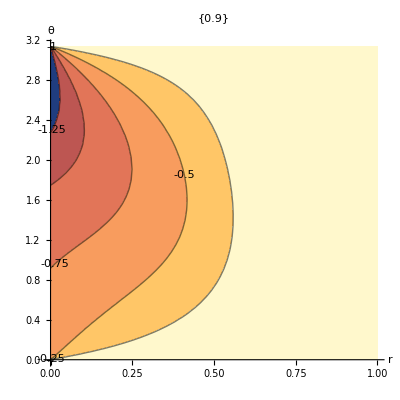
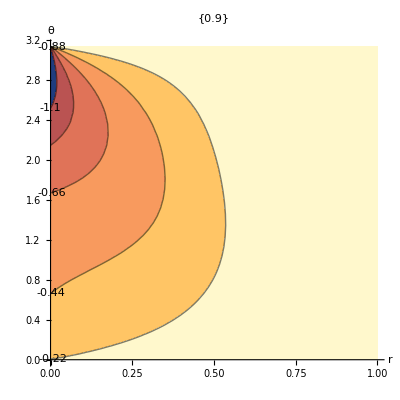
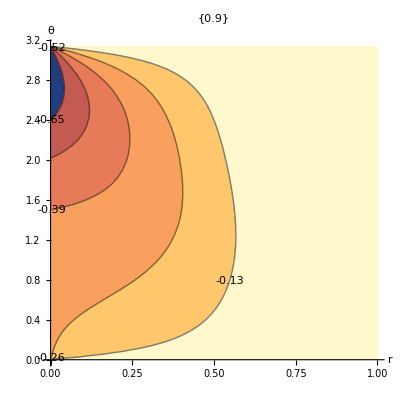
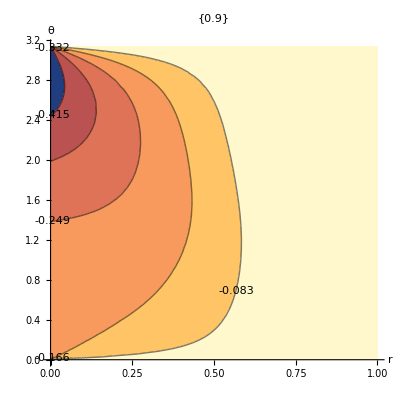
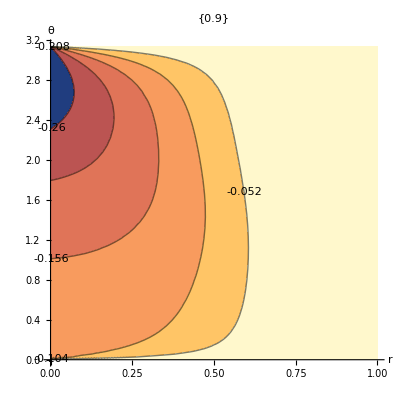
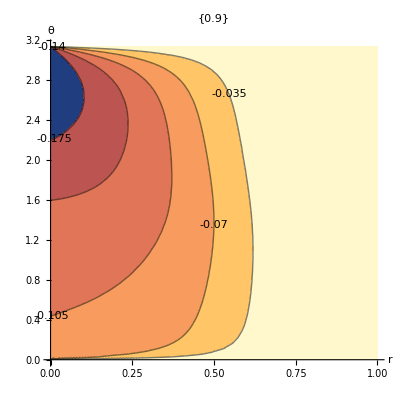
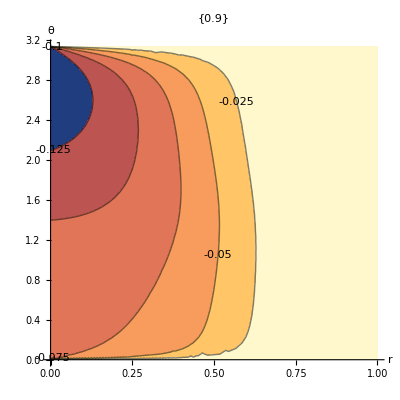
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ContourPlot[hPlus[KBmetricPlus]/.{M-> 1,a->atest,j->jtest},{Rr,0,1},{θ,0,π},Frame-> False, Axes-> True,ContourLabels-> All,ContourShading->Automatic,Contours->5,AxesLabel->{r,θ},PlotLabel->{atest}],{atest,0.9,1,0.01},{jtest,0,1,0.1}]
```

```mathematica
Table[ContourPlot[hPlus[KBmetricPlus]/.{M-> 1,a->0.9,j-> jtest},{Rr,0,20},{θ,0,π},Frame-> False, Axes-> True,ContourLabels-> All,ContourShading->None,AxesLabel->{r,θ},Mesh->Full,PlotLegends->Automatic,PlotLabel->jtest],{jtest,0,4,0.5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Schwarzschild Black Hole in a Swirling Universe

```mathematica
Block[{rPlus,rMinus,hPlus,hMinus,M},Clear["Global`*"]]
(*Setting a =0 to recover the Schwarzschild Black Hole*)
a=0;
F = 1+j^2 r^4 Cos[θ]^4;
rs = 1-(2M)/r;
Δ = 4j(r-2M)Cos[θ];
coordinates = {t,r,θ,ϕ};
SBHmetricPlus = Simplify[{{(r^2 Sin[θ]^2)/F-F*rs,0,0,(r^2 Sin[θ]^2 Δ)/F},{0,F/rs,0,0},{0,0,F r^2,0},{(r^2 Sin[θ]^2 Δ)/F,0,0,(r^2 Sin[θ]^2)/F}}/.r-> rPlus];
Table[ContourPlot[hPlus[SBHmetricPlus]/.{j-> jtest},{Rr,5,10},{θ,0,π},Frame-> False, Axes-> True,Contours->Array[If[#>0,{#,Blue},{#,Red}]&,40,{-30,10}],ContourShading->None,PlotLegends->Automatic,FrameLabel->{"R","θ"},Mesh->Full,PlotLabel->jtest],{jtest,0,4,0.5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}